# Data Set 5

```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;

set=5;
```

## Data Import

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
02/10/2016 08:09:32
$MEAS_TIM:
86400 94490
$DATA:
0 8191
       0
       0
       0

2
       9
$ROI:
0
$PRESETS:
Live Time
86400
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

\begin{array}{c}
 \text{$\$$SPEC$\_$ID:} \\
 \text{Molnar Range} \\
 \text{$\$$SPEC$\_$REM:} \\
 \text{DET$\#$ 1} \\
 \text{DETDESC$\#$ HPGe Detector 1} \\
 \text{AP$\#$ GammaVision Version 6.07} \\
 \text{$\$$DATE$\_$MEA:} \\
 \text{02/10/2016 08:09:32} \\
 \text{$\$$MEAS$\_$TIM:} \\
 \text{86400 94490} \\
 \text{$\$$DATA:} \\
 \text{0 8191} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{       2} \\
 \text{       9} \\
 \text{$\$$ROI:} \\
 0 \\
 \text{$\$$PRESETS:} \\
 \text{Live Time} \\
 86400 \\
 0 \\
 \text{$\$$ENER$\_$FIT:} \\
 \text{0.137869 0.366631} \\
 \text{$\$$MCA$\_$CAL:} \\
 3 \\
 \text{1.378689E-001 3.666307E-001 -4.415950E-008 keV} \\
 \text{$\$$SHAPE$\_$CAL:} \\
 3 \\
 \text{2.301834E+000 9.195991E-004 -5.357180E-008} \\
\end{array}

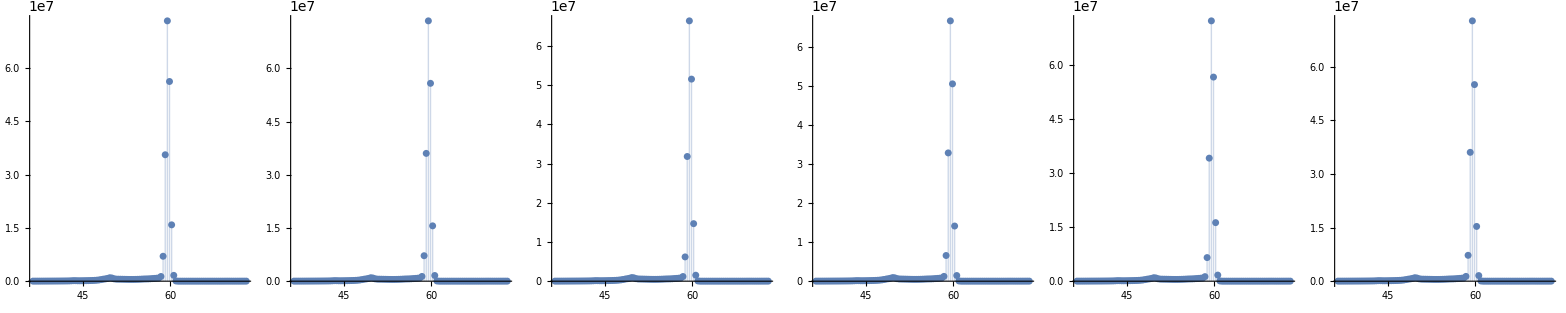

```mathematica
filenames={
"Am-241-24hr-NewConfiguration.Spe",
"Am-241-24hr-NewConfiguration-2.Spe",
"Am-241-24hr-ThickFilm-NewConfiguration.Spe",
"Am-241-24hr-ThickFilm-NewConfiguration-2.Spe",
"Am-241-24hr-ThinFilm-NewConfiguration.Spe",
"Am-241-24hr-ThinFilm-NewConfiguration-2.Spe"};

m=Length[filenames];
For[n=1,n≤m,n++,
imported=Import[filenames[[n]],"Data"];
times=ToExpression[StringSplit[imported[[10]]]];
If[n==2,
Print[TableForm[imported[[;;15]]]];
Print[TableForm[imported[[-16;;]]]];
Print[TeXForm[TableForm[Drop[imported,{16,Length[imported]-16}]]]];
];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
energy[n]=ToExpression[StringSplit[imported[[-7]]]];
data[n]=Table[{i,energy[n][[1]]+energy[n][[2]](i-1),freq[[i]]},{i,Length[freq]}];
]
Grid[{Table[ListPlot[data[i][[100;;200,{2,3}]],ImageSize->Medium,PlotRange->All,Filling->Bottom],{i,1,m}]}]
Clear[n,filenames,imported,times,deadtime,freq]
```

## Data Analysis

## Equations

```mathematica
F[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
G[x_,mu_,sigma_,a_]:=Sum[F[x,mu[[i]],sigma[[i]],a[[i]]],{i,1,Length[mu]}]
fwhm[sigma_]:=2*sigma*Sqrt[2*Log[2]];

err[F_,w__]:={F[Map[First,List[w]]/.List->Sequence],Block[{parms=Table[Unique[],{x,1,Length[List[w]]}],values=Table[List[w][[i,1]],{i,1,Length[List[w]]}],errors=Table[List[w][[i,2]],{i,1,Length[List[w]]}]},Sqrt[Total[Table[(D[F[parms/.List->Sequence],parms[[i]]]*errors[[i]])^2,{i,1,Length[values]}]/.Table[parms[[i]]->values[[i]],{i,1,Length[values]}]]]]}
```

## Cubic Fit

| Estimate | Standard Error | t-Statistic | P-Value
a | -5.51365×10^6 | 2.21835×10^6 | -2.48547 | 0.0418733
b | 9.65732×10^8 | 3.901×10^8 | 2.4756 | 0.0424828
c | -5.63552×10^10 | 2.2859×10^10 | -2.46534 | 0.0431266
d | 1.09566×10^12 | 4.46351×10^11 | 2.45471 | 0.0438035
mu | 61.5734 | 9.48465×10^-94 | 6.4919×10^94 | 5.43466435138132×10^-662
sigma | -0.0246702 | 2.20986×10^-92 | -1.11637×10^90 | 1.22213645580606×10^-628
p | 7.46331×10^7 | 1.34561×10^-104 | 5.54642×10^111 | 1.63563605414012×10^-780

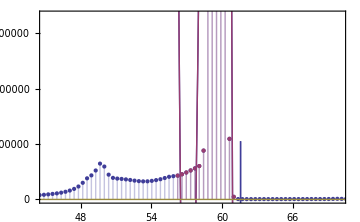

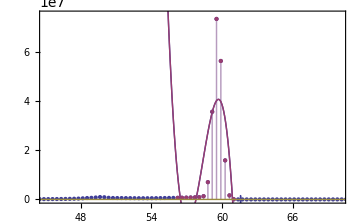

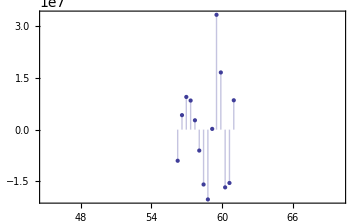

```mathematica
region={154,167};
Clear[a,b,c,d,mu,sigma,p]
viewingregion={50,200};viewingrange={45,70};imagesize=Medium;fontsize=12;theme="Classic";

guess={{a,361},{b,-61524},{c,3473469},{d,-65035121},{mu,59.6},{sigma,0.37},{p,670000}};

k=1;
cubic[k]=NonlinearModelFit[data[k][[region[[1]];;region[[2]],{2,3}]],a x^3+b x^2+c x+d+F[x,mu,sigma,p],guess,x];

cubic[k]["ParameterTable"]
cubicparams[k]=cubic[k]["BestFitParameters"][[All,2]];

Show[ListPlot[{data[k][[viewingregion[[1]];;viewingregion[[2]],{2,3}]],data[k][[region[[1]];;region[[2]],{2,3}]]},Filling->Axis,PlotRange->All,PlotTheme->theme],Plot[{cubic[k]["BestFit"],cubicparams[k][[1]]x^3+cubicparams[k][[2]]x^2+cubicparams[k][[3]]x+cubicparams[k][[4]],F[x,cubicparams[k][[-3]],cubicparams[k][[-2]],cubicparams[k][[-1]]]},{x,-10,100},PlotTheme->theme],PlotRange->{viewingrange,{0,5000000}},Frame->{{True,False},{True,False}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]

Show[ListPlot[{data[k][[viewingregion[[1]];;viewingregion[[2]],{2,3}]],data[k][[region[[1]];;region[[2]],{2,3}]]},Filling->Axis,PlotRange->All,PlotTheme->theme],Plot[{cubic[k]["BestFit"],cubicparams[k][[1]]x^3+cubicparams[k][[2]]x^2+cubicparams[k][[3]]x+cubicparams[k][[4]],F[x,cubicparams[k][[-3]],cubicparams[k][[-2]],cubicparams[k][[-1]]]},{x,-10,100},PlotTheme->theme],PlotRange->{viewingrange,{0,75000000}},Frame->{{True,False},{True,False}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]

ListPlot[Join[Table[{energy[k][[1]]+energy[k][[2]](i-1)},{i,region[[1]],region[[2]]}],Transpose[{cubic[k]["FitResiduals"]}],2],Filling->Axis,Frame->{{True,False},{True,False}},FrameTicks->{{True,False},{True,False}},Axes->True,PlotRange->{viewingrange,All},PlotTheme->theme,ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]
```

## Gaussian Fits

```mathematica
mu={24.1,26.4,51.6,49.6,56.7,58.6,59.6};
sigma={0.6,0.4,4.0,0.7,1.4,0.8,0.36};
a={2000,5000,18000,18000,16000,24000,2900000}*10;
n=Length[mu];region={1,3000};
symbol={"μ","σ","a","I"};

For[k=1,k≤m,k++,
model[k]=NonlinearModelFit[data[k][[region[[1]];;region[[2]],{2,3}]],G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
params[k]=model[k]["BestFitParameters"][[All,2]];
paramerrors[k]=model[k]["ParameterErrors"];

modeldata=Table[err[F,{i,0},{params[k][[n]],paramerrors[k][[n]]},{params[k][[2n]],paramerrors[k][[2n]]},{params[k][[3n]],paramerrors[k][[3n]]}],{i,Table[data[k][[i[[1]],2]],{i,Position[data[k][[;;200,2]],_?(params[k][[n]]-2*fwhm[params[k][[2n]]]<#<params[k][[n]]+2*fwhm[params[k][[2n]]]&)]}]}];
intensity[k]={Total[modeldata[[All,1]]*energy[k][[2]]],Sqrt[Total[(modeldata[[All,2]]*energy[k][[2]])^2]]};
Print[TableForm[Insert[Insert[

Table[{symbol[[i/n]],params[k][[i]],paramerrors[k][[i]],100*paramerrors[k][[i]]/params[k][[i]]},{i,{n,2n,3n}}],

Join[{symbol[[4]]},intensity[k],{100*intensity[k][[2]]/intensity[k][[1]]}],4]
,{{},{"Value"},{"Error"},{"Percent Error"}},1]]];
];
```

| Value | Error | Percent Error
μ | 59.6183 | 0.000138411 | 0.000232162
σ | 0.36654 | 0.000243978 | 0.0665624
a | 7.49903×10^7 | 86408.9 | 0.115227
I | 6.88992×10^7 | 48160.6 | 0.0699001

| Value | Error | Percent Error
μ | 59.6147 | 0.000141699 | 0.000237692
σ | 0.366783 | 0.000248354 | 0.0677112
a | 7.49345×10^7 | 89529.9 | 0.119478
I | 6.88937×10^7 | 49711.9 | 0.0721574

| Value | Error | Percent Error
μ | 59.6229 | 0.000148152 | 0.000248482
σ | 0.366042 | 0.000254308 | 0.0694752
a | 6.81346×10^7 | 83112.4 | 0.121983
I | 6.25152×10^7 | 46188.3 | 0.0738833

| Value | Error | Percent Error
μ | 59.6137 | 0.00014712 | 0.000246789
σ | 0.367019 | 0.000257137 | 0.0700609
a | 6.80396×10^7 | 84545.5 | 0.124259
I | 6.25948×10^7 | 46910.9 | 0.0749437

| Value | Error | Percent Error
μ | 59.6269 | 0.00013648 | 0.00022889
σ | 0.365495 | 0.000237456 | 0.0649685
a | 7.44337×10^7 | 81471.5 | 0.109455
I | 6.81927×10^7 | 45657.5 | 0.0669536

| Value | Error | Percent Error
μ | 59.6122 | 0.000140669 | 0.000235973
σ | 0.367166 | 0.000247627 | 0.0674427
a | 7.42027×10^7 | 87919.5 | 0.118486
I | 6.82921×10^7 | 48884.8 | 0.0715819

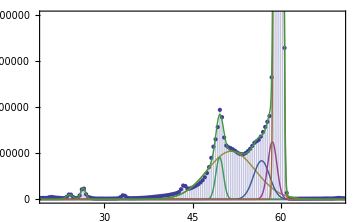
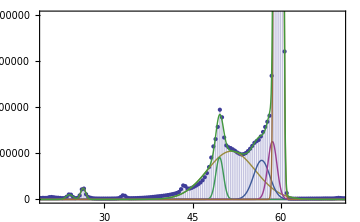
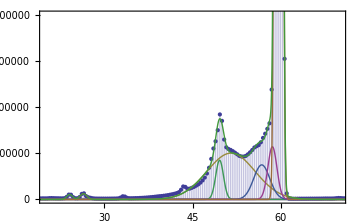
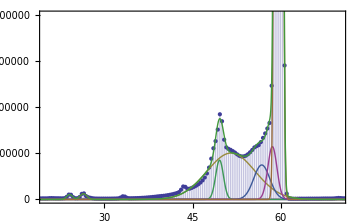
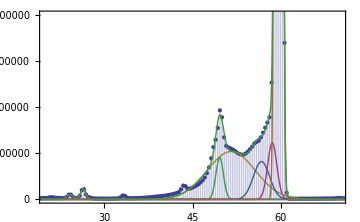
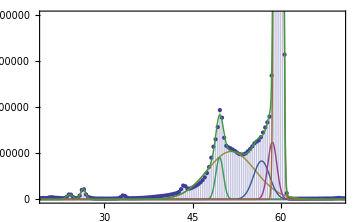
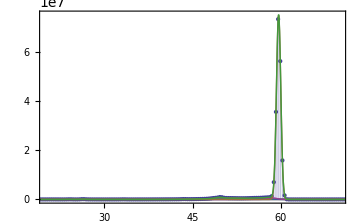
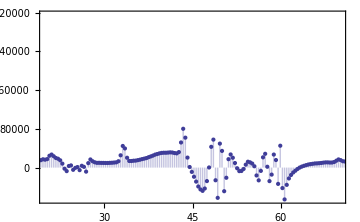
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- -Graphics- | -Graphics- -Graphics- | -Graphics- -Graphics- | -Graphics- -Graphics- | -Graphics- -Graphics- | -Graphics- -Graphics-

```mathematica
viewingrange={20,70};
theme="Classic";imagesize=Medium;fontsize=12;

Grid[Transpose[Table[{Show[ListPlot[data[k][[region[[1]];;region[[2]],{2,3}]],Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[k][[i]],params[k][[i+n]],params[k][[i+2n]]],{i,1,n}],{G[x,params[k][[;;n]],params[k][[n+1;;2n]],params[k][[2n+1;;3n]]]}],{x,-10,200},PlotRange->All,PlotTheme->theme],Frame->{{True,False},{True,False}},PlotRange->{viewingrange,{0,2000000}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}],

Show[ListPlot[data[k][[region[[1]];;region[[2]],{2,3}]],Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[k][[i]],params[k][[i+n]],params[k][[i+2n]]],{i,1,n}],{G[x,params[k][[;;n]],params[k][[n+1;;2n]],params[k][[2n+1;;3n]]]}],{x,-10,200},PlotRange->All,PlotTheme->theme],Frame->{{True,False},{True,False}},PlotRange->{viewingrange,All},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]

ListPlot[Join[Table[{energy[k][[1]]+energy[k][[2]](i-1)},{i,region[[1]],region[[2]]}],Transpose[{model[k]["FitResiduals"]}],2],Filling->Axis,Frame->{{True,False},{True,False}},FrameTicks->{{True,False},{True,False}},Axes->True,PlotRange->{viewingrange,All},PlotTheme->theme,ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]},{k,1,m}]]]
```

```mathematica
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;
runs={"Source 1","Source 2","Thick 1","Thick 2","Thin 1", "Thin 2"};
thickness={40,0.01};

Print[TableForm[Insert[Table[Join[{runs[[i]]},intensity[i],{100*intensity[i][[2]]/intensity[i][[1]]}],{i,1,m}],{{},{"Intensity"},{"Error"},"Percent Error"},1]]]

Print["\nTrial 1"]
atten=err[coeff,intensity[1],intensity[3],thickness];
Print["attenuation coefficient = ",Join[atten,{100*atten[[2]]/atten[[1]]}]]
thin=err[coeff,intensity[1],intensity[5],atten];Print["thin foil measurement = ",Join[thin,{100*thin[[2]]/thin[[1]]}]]

Print["\nTrial 2"]
atten=err[coeff,intensity[2],intensity[4],thickness];
Print["attenuation coefficient = ",Join[atten,{100*atten[[2]]/atten[[1]]}]]
thin=err[coeff,intensity[2],intensity[6],atten];Print["thin foil measurement = ",Join[thin,{100*thin[[2]]/thin[[1]]}]]
```

| Intensity | Error | Percent Error
Source 1 | 6.88992×10^7 | 48160.6 | 0.0699001
Source 2 | 6.88937×10^7 | 49711.9 | 0.0721574
Thick 1 | 6.25152×10^7 | 46188.3 | 0.0738833
Thick 2 | 6.25948×10^7 | 46910.9 | 0.0749437
Thin 1 | 6.81927×10^7 | 45657.5 | 0.0669536
Thin 2 | 6.82921×10^7 | 48884.8 | 0.0715819

Trial 1

attenuation coefficient = {0.00243086,0.0000254346,1.04632}

thin foil measurement = {4.24006,0.400647,9.44909}

Trial 2

attenuation coefficient = {0.00239706,0.0000260156,1.08531}

thin foil measurement = {3.65894,0.425874,11.6393}